# ODE simulation RESEAU BOOLEEN TRAYNARD EXEMPLE

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
<<BooleanToLogisticODE`
```

```mathematica
Unprotect[t];Clear[t];Protect[t];
```

## RESEAU BOOLEEN EXEMPLE

```mathematica
FB= {Cdc20->CycB,Cdh1->(!CycA&&!CycB)||p27,CycA->(!Cdc20&&!Cdh1&&CycA)||(!Cdc20&&!Cdh1&&E2F&&!Rb)||(CycA&&!UbcH10)||(E2F&&!Rb&&!UbcH10),CycB->(!Cdc20&&!Cdh1)||(!Cdh1&&!UbcH10),CycE->E2F&&!Rb,E2F->(!Cdc20&&!CycA&&!Rb)||(!Cdc20&&p27&&!Rb)||(!CycA&&!CycB&&!Rb)||(!CycB&&p27&&!Rb),p27->(!CycA&&!CycB&&!CycD&&!CycE)||(!CycA&&!CycB&&!CycD&&p27)||(!CycB&&!CycD&&!CycE&&p27)||(!CycD&&!Skp2),Rb->(!CycA&&!CycB&&!CycD&&!CycE)||(!CycA&&!CycD&&p27)||(!CycB&&!CycD&&p27)||(!CycD&&!CycE&&p27),Skp2->!Cdh1||!Rb,UbcH10->(Cdc20&&UbcH10)||!Cdh1||(CycA&&UbcH10)||(CycB&&UbcH10),CycD->CycD};
```

Reduce each Boolean rule to its minimal disjunctive normal form (the built-in BooleanMinimize) BEFORE translating it to ODEs. This canonicalisation is intentional and is not part of the De Morgan map: BooleanToOdeSystem below is a pure translator. For this network the rules are already in minimal DNF, so FBmin coincides with FB.

```mathematica
FBmin=FB/.(lhs_->rhs_):>(lhs->BooleanMinimize[rhs,"DNF"])
```

{Cdc20→CycB,Cdh1→(!CycA&&!CycB)||p27,CycA→(!Cdc20&&!Cdh1&&CycA)||(!Cdc20&&!Cdh1&&E2F&&!Rb)||(CycA&&!UbcH10)||(E2F&&!Rb&&!UbcH10),CycB→(!Cdc20&&!Cdh1)||(!Cdh1&&!UbcH10),CycE→E2F&&!Rb,E2F→(!Cdc20&&!CycA&&!Rb)||(!Cdc20&&p27&&!Rb)||(!CycA&&!CycB&&!Rb)||(!CycB&&p27&&!Rb),p27→(!CycA&&!CycB&&!CycD&&!CycE)||(!CycA&&!CycB&&!CycD&&p27)||(!CycB&&!CycD&&!CycE&&p27)||(!CycD&&!Skp2),Rb→(!CycA&&!CycB&&!CycD&&!CycE)||(!CycA&&!CycD&&p27)||(!CycB&&!CycD&&p27)||(!CycD&&!CycE&&p27),Skp2→!Cdh1||!Rb,UbcH10→(Cdc20&&UbcH10)||!Cdh1||(CycA&&UbcH10)||(CycB&&UbcH10),CycD→CycD}

```mathematica
(*generateur de reference-- re-executer pour un nouveau tirage*)
κ = AssociationThread[Keys[FB], RandomReal[{50, 100}, Length[Keys[FB]]]];
 γ = AssociationThread[Keys[FB], RandomReal[{0.25, 2}, Length[Keys[FB]]]];
 θ = AssociationThread[Keys[FB], Array[15 + RandomReal[{-5, 5}] &, Length[Keys[FB]]]];
 n = RandomInteger[{1, 60}];
initialcondition = AssociationThread[Keys[FB], RandomReal[{0, 100}, Length[Keys[FB]]]];
```

```mathematica
κ = <|Cdc20 -> 74.3265, Cdh1 -> 61.0013, CycA -> 79.1737, CycB -> 76.701, CycE -> 91.0648, E2F -> 56.497, p27 -> 68.7935, Rb -> 53.2028, Skp2 -> 66.6451, UbcH10 -> 73.5135, CycD -> 64.7453|>
```

<|Cdc20→74.3265,Cdh1→61.0013,CycA→79.1737,CycB→76.701,CycE→91.0648,E2F→56.497,p27→68.7935,Rb→53.2028,Skp2→66.6451,UbcH10→73.5135,CycD→64.7453|>

```mathematica
γ =  <|Cdc20 -> 0.701777, Cdh1 -> 1.44791, CycA -> 1.74028, CycB -> 0.939896, CycE -> 0.581402, E2F -> 0.575771, p27 -> 0.678557, Rb -> 1.23997, Skp2 -> 0.42572, UbcH10 -> 1.95187, CycD -> 0.763729|>
```

<|Cdc20→0.701777,Cdh1→1.44791,CycA→1.74028,CycB→0.939896,CycE→0.581402,E2F→0.575771,p27→0.678557,Rb→1.23997,Skp2→0.42572,UbcH10→1.95187,CycD→0.763729|>

```mathematica
θ = <|Cdc20 -> 19.1793, Cdh1 -> 11.8373, CycA -> 19.2931, CycB -> 18.8364, CycE -> 18.9019, E2F -> 17.2991, p27 -> 14.6859, Rb -> 11.7336, Skp2 -> 12.9523, UbcH10 -> 12.0482, CycD -> 19.891|>
```

<|Cdc20→19.1793,Cdh1→11.8373,CycA→19.2931,CycB→18.8364,CycE→18.9019,E2F→17.2991,p27→14.6859,Rb→11.7336,Skp2→12.9523,UbcH10→12.0482,CycD→19.891|>

```mathematica
n = 4
```

4

```mathematica
initialcondition =<|Cdc20->19.1793,Cdh1->11.8373,CycA->19.2931,CycB->18.8364,CycE->18.9019,E2F->17.2991,p27->14.6859,Rb->11.7336,Skp2->12.9523,UbcH10->12.0482,CycD->19.891|>
```

<|Cdc20→19.1793,Cdh1→11.8373,CycA→19.2931,CycB→18.8364,CycE→18.9019,E2F→17.2991,p27→14.6859,Rb→11.7336,Skp2→12.9523,UbcH10→12.0482,CycD→19.891|>

```mathematica
κ=Map[Round[#,0.01]&,κ]
γ=Map[Round[#,0.01]&,γ]
θ=Map[Round[#,0.01]&,θ]
initialcondition =Map[Round[#,0.01]&,initialcondition]
```

<|Cdc20→74.33,Cdh1→61.,CycA→79.17,CycB→76.7,CycE→91.06,E2F→56.5,p27→68.79,Rb→53.2,Skp2→66.65,UbcH10→73.51,CycD→64.75|>

<|Cdc20→0.7,Cdh1→1.45,CycA→1.74,CycB→0.94,CycE→0.58,E2F→0.58,p27→0.68,Rb→1.24,Skp2→0.43,UbcH10→1.95,CycD→0.76|>

<|Cdc20→19.18,Cdh1→11.84,CycA→19.29,CycB→18.84,CycE→18.9,E2F→17.3,p27→14.69,Rb→11.73,Skp2→12.95,UbcH10→12.05,CycD→19.89|>

<|Cdc20→19.18,Cdh1→11.84,CycA→19.29,CycB→18.84,CycE→18.9,E2F→17.3,p27→14.69,Rb→11.73,Skp2→12.95,UbcH10→12.05,CycD→19.89|>

#### ODE

```mathematica
Framed@TableForm[
system1=BooleanToOdeSystem[FBmin,t,κ,γ,θ,n,initialcondition,{logisticm,logisticp}]]
```

Cdc20'[t]==-0.7 Cdc20[t]+74.33 logisticp[CycB[t],18.84,4]
Cdc20[0]==19.18
Cdh1'[t]==-1.45 Cdh1[t]+61. (1-(1-logisticm[CycA[t],19.29,4] logisticm[CycB[t],18.84,4]) logisticm[p27[t],14.69,4])
Cdh1[0]==11.84
CycA'[t]==-1.74 CycA[t]+79.17 (1-(1-logisticm[Cdc20[t],19.18,4] logisticm[Cdh1[t],11.84,4] logisticp[CycA[t],19.29,4]) (1-logisticm[UbcH10[t],12.05,4] logisticp[CycA[t],19.29,4]) (1-logisticm[Cdc20[t],19.18,4] logisticm[Cdh1[t],11.84,4] logisticm[Rb[t],11.73,4] logisticp[E2F[t],17.3,4]) (1-logisticm[Rb[t],11.73,4] logisticm[UbcH10[t],12.05,4] logisticp[E2F[t],17.3,4]))
CycA[0]==19.29
CycB'[t]==-0.94 CycB[t]+76.7 (1-(1-logisticm[Cdc20[t],19.18,4] logisticm[Cdh1[t],11.84,4]) (1-logisticm[Cdh1[t],11.84,4] logisticm[UbcH10[t],12.05,4]))
CycB[0]==18.84
CycE'[t]==-0.58 CycE[t]+91.06 logisticm[Rb[t],11.73,4] logisticp[E2F[t],17.3,4]
CycE[0]==18.9
E2F'[t]==-0.58 E2F[t]+56.5 (1-(1-logisticm[Cdc20[t],19.18,4] logisticm[CycA[t],19.29,4] logisticm[Rb[t],11.73,4]) (1-logisticm[CycA[t],19.29,4] logisticm[CycB[t],18.84,4] logisticm[Rb[t],11.73,4]) (1-logisticm[Cdc20[t],19.18,4] logisticm[Rb[t],11.73,4] logisticp[p27[t],14.69,4]) (1-logisticm[CycB[t],18.84,4] logisticm[Rb[t],11.73,4] logisticp[p27[t],14.69,4]))
E2F[0]==17.3
p27'[t]==68.79 (1-(1-logisticm[CycA[t],19.29,4] logisticm[CycB[t],18.84,4] logisticm[CycD[t],19.89,4] logisticm[CycE[t],18.9,4]) (1-logisticm[CycD[t],19.89,4] logisticm[Skp2[t],12.95,4]) (1-logisticm[CycA[t],19.29,4] logisticm[CycB[t],18.84,4] logisticm[CycD[t],19.89,4] logisticp[p27[t],14.69,4]) (1-logisticm[CycB[t],18.84,4] logisticm[CycD[t],19.89,4] logisticm[CycE[t],18.9,4] logisticp[p27[t],14.69,4]))-0.68 p27[t]
p27[0]==14.69
Rb'[t]==53.2 (1-(1-logisticm[CycA[t],19.29,4] logisticm[CycB[t],18.84,4] logisticm[CycD[t],19.89,4] logisticm[CycE[t],18.9,4]) (1-logisticm[CycA[t],19.29,4] logisticm[CycD[t],19.89,4] logisticp[p27[t],14.69,4]) (1-logisticm[CycB[t],18.84,4] logisticm[CycD[t],19.89,4] logisticp[p27[t],14.69,4]) (1-logisticm[CycD[t],19.89,4] logisticm[CycE[t],18.9,4] logisticp[p27[t],14.69,4]))-1.24 Rb[t]
Rb[0]==11.73
Skp2'[t]==66.65 (1-logisticp[Cdh1[t],11.84,4] logisticp[Rb[t],11.73,4])-0.43 Skp2[t]
Skp2[0]==12.95
UbcH10'[t]==73.51 (1-logisticp[Cdh1[t],11.84,4] (1-logisticp[Cdc20[t],19.18,4] logisticp[UbcH10[t],12.05,4]) (1-logisticp[CycA[t],19.29,4] logisticp[UbcH10[t],12.05,4]) (1-logisticp[CycB[t],18.84,4] logisticp[UbcH10[t],12.05,4]))-1.95 UbcH10[t]
UbcH10[0]==12.05
CycD'[t]==-0.76 CycD[t]+64.75 logisticp[CycD[t],19.89,4]
CycD[0]==19.89

```mathematica
fun=#[t]&/@Keys[FB];
```

```mathematica
S=NDSolve[system1,Keys[FB],{t,0,60}];
```

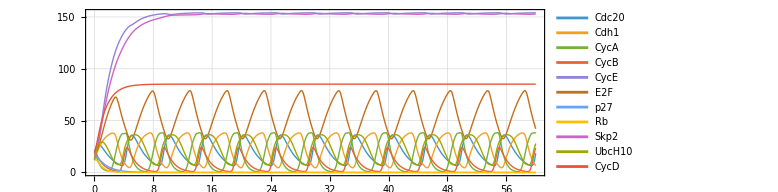

```mathematica
GG1=Plot[Evaluate[fun/.NDSolve[system1,Keys[FB],{t,0,60}]],{t,0,60}, PlotRange->All, PlotTheme->"Detailed",PlotStyle->Thick,PlotLegends->Placed[Keys[FB],Right],LabelStyle->Directive[FontFamily->"Franklin Gothic",11],
AspectRatio->1/3, PlotLabel->"", ImageSize->Large]
```

```mathematica
Export["TTRAYNARD_EXEMPLE.jpeg",GG1,ImageResolution->300]
```

TTRAYNARD_EXEMPLE.jpeg